```mathematica
ex1=Grid[{{
-Graphics-,
Spacer[1],
Style[
(*Column[{ 
Item[ButtonBar[{Graphics[{Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}]},ImageSize->20]:>FrontEndTokenExecute[InputNotebook[],"SelectionOpenAllGroups"],Graphics[{Polygon[{{1,Sqrt[3]},{0,0},{-1,Sqrt[3]}}]},ImageSize->20]:>FrontEndTokenExecute[InputNotebook[],"SelectionCloseAllGroups"]
},Background->RGBColor[0.811765,0.721569,0.486275]],Alignment->Center],*)
Column[{
ActionMenu[Style[" Contents ",16],{
Style["Ideal Solutions",Bold,15]:>NotebookLocate["Ideal Solutions"],
Framed@Style["Pressure-Composition Diagrams (P-x-y)",Bold,14]:>NotebookLocate["Pressure-Composition Diagrams"],
Style["Raoult's Law",Bold,Italic,13]:>NotebookLocate["Raoult's Law"],
Row[{Style["Screencast:",Bold]," Raoult's Law"}]:>NotebookLocate["link 1"],
"💡 Derivation of Raoult's Law":>NotebookLocate["Derivation of Raoult's Law"],
Style["Mapping a P-x-y Diagram",Bold,Italic,13]:>NotebookLocate["Mapping a P-x-y Diagram"],
Style["Figure 1",Italic]:>NotebookLocate["Figure 1"],
Style["Lever Rule",Bold,Italic,13]:>NotebookLocate["Lever Rule"],
Row[{Style["Screencast:",Bold]," Lever Rule"}]:>NotebookLocate["link 2"],
Style["Figure 2",Italic]:>NotebookLocate["Figure 2"],
"Test Yourself":>NotebookLocate["Concept Test 1"],
"💡 Solution":>NotebookLocate["Solution 1"],
Style["Figure 3",Italic]:>NotebookLocate["Figure 3"],
Style["Changes in Pressure",Bold,Italic,13]:>NotebookLocate["Changes in Pressure"],
"Effect on Liquid and Vapor Amounts (Lever Rule)":>NotebookLocate["Effect on Liquid and Vapor Amounts (Lever Rule)"],
Style["Figure 4",Italic]:>NotebookLocate["Figure 4"],
"Effect on Molar Composition in the Liquid and Vapor Phases":>NotebookLocate["Effect on Molar Composition in the Liquid and Vapor Phases"],
"Test Yourself":>NotebookLocate["Concept Test 2"],
Style["Figure 5",Italic]:>NotebookLocate["Figure 5"],
Style["Figure 6",Italic]:>NotebookLocate["Figure 6"],
Row[{Style["Screencast:",Bold]," Add a Component to Binary system in VLE"}]:>NotebookLocate["link 3"],
"Test Yourself":>NotebookLocate["Concept Test 3"],
Style["Figure 7",Italic]:>NotebookLocate["Figure 7"],
Style["Changes in Temperature",Bold,Italic,13]:>NotebookLocate["Changes in Temperature"],
"Exercise 1":>NotebookLocate["Exercise 1"],
Style["Figure 8",Italic]:>NotebookLocate["Figure 8"],
"Test Yourself":>NotebookLocate["Concept Test 4"],
"💡 Solution":>NotebookLocate["Solution 4"],
Style["Figure 9",Italic]:>NotebookLocate["Figure 9"],
"Test Yourself":>NotebookLocate["Concept Test 5"],
Style["Figure 10",Italic]:>NotebookLocate["Figure 10"],
"Test Yourself":>NotebookLocate["Concept Test 6"],
Style["Figure 11",Italic]:>NotebookLocate["Figure 11"],
Framed@Style["Temperature-Composition Diagrams (T-x-y)",Bold,14]:>NotebookLocate["Temperature-Composition Diagrams"],
Style["Raoult's Law",Bold,Italic,13]:>NotebookLocate["Raoult's Law T-x-y"],
Style["Figure 12",Italic]:>NotebookLocate["Figure 12"],
Row[{Style["Screencast:",Bold]," Bubble Temperature: Raoult's Law"}]:>NotebookLocate["link 4"],
Style["Mapping a T-x-y Diagram",Bold,Italic,13]:>NotebookLocate["Mapping a T-x-y Diagram"],
Style["Figure 13",Italic]:>NotebookLocate["Figure 13"],
Style["Changes in Temperature",Bold,Italic,13]:>NotebookLocate["Changes in Temperature T-x-y"],
"Effect on Liquid and Vapor Amounts (Lever Rule)":>NotebookLocate["Effect on Liquid and Vapor Amounts (Lever Rule) T-x-y"],
Style["Figure 14",Italic]:>NotebookLocate["Figure 14"],
Row[{Style["Screencast:",Bold]," T-x-y Diagram: Lever Rule (Review)"}]:>NotebookLocate["link 5"],
"Effect on Molar Composition in the Liquid and Vapor Phases":>NotebookLocate["Effect on Molar Composition in the Liquid and Vapor Phases T-x-y"],
"Test Yourself":>NotebookLocate["Concept Test 7"],
Style["Figure 15",Italic]:>NotebookLocate["Figure 15"],
Style["Figure 16",Italic]:>NotebookLocate["Figure 16"],
Row[{Style["Screencast:",Bold]," Phase Equilibrium: T-x-y Diagram"}]:>NotebookLocate["link 6"],
"Adding Energy to a System":>NotebookLocate["Adding Energy to a System"],
Style["Figure 17",Italic]:>NotebookLocate["Figure 17"],
Style["Changes in Pressure",Bold,Italic,13]:>NotebookLocate["Changes in Pressure T-x-y"],
"Test Yourself":>NotebookLocate["Concept Test 8"],
Style["Figure 18",Italic]:>NotebookLocate["Figure 18"]
},Background->RGBColor[0.811765,0.721569,0.486275]]
(*},Alignment->Left]*),Text@Style["Baumann,  Falconer,  Nicodemus",White,Bold,13,FontFamily->"Arial"]}],
FontFamily->"Arial"]
}},ItemSize->{{38,20}}];

SetOptions[EvaluationNotebook[],{DockedCells->Cell[BoxData[ToBoxes[ex1]/.{(ImageSize->{___,___})->(ImageSize->{1399,10})}],"DockedCell",Background->Black,ImageMargins->0,CellMargins->{{0,0},{0,0}},CellFrameMargins->{{0,0},{0,0}}]}
];
```

# Vapor-Liquid Equilibrium (VLE) for Ideal Solutions

## Objectives

●  Be able to apply Raoult’s law to vapor-liquid equilibrium

●  Understand what P-x-y and T-x-y diagrams represent and be able to use to solve VLE problems

## I don’t think there is any reason to make the objectives not visible. Seems like we should only use this option when want to hide details.

## Also, I dont want the big fonts like were in the previous version. I tried to change them.

## Pressure-Composition (P-x-y) Diagrams

The Gibbs’ phase rule is used to determine the number of degrees of freedom for a non-reactive system:

F=C-P+2

where F is the number of degrees of freedom, C is the number of components, and P is the number of phases. For a single component (C=1) at vapor-liquid equilibrium (P=2), then F=1-2+2=1. If pressure is fixed, then the boiling temperature is fixed, and all the liquid boils at the same temperature. For a binary mixture (C=2) in VLE (P=2), F=2-2+2=2, so that if the temperature if fixed, the pressure can be changed and still maintain VLE. When the pressure changes, the compositions of the liquid and vapor also change.

## Raoult’s Law

The mole fractions in the liquid and vapor phases that are in equilibrium are given by Raoult's law:

## in the gray section for the equations. We need to make this a much lighter color of gray so that the contrast is better or perhaps we should discuss if anohter color is better.

## I dont understand the caret on the left of Raoult’s law. Seems like it just removes one line. Why is it there?

x_i P_i^sat=y_i P

where x_i represents the mole fraction of component i in the liquid phase and y_i represents the mole fraction in the vapor phase, and P is the total pressure. P_i^sat is the saturation pressure, which can be calculated using an Antoine equation.

log_10(P_i^sat)=A_i-B_i/(T+C_i)

A_i, B_i, and C_i are Antoine constants for a given component. For a fixed temperature, the pressure at which vapor first appears is called the bubble-point (BP) pressure.

P_BP=P ∑y_i=y_1 P+y_2 P

That is, the sum of the partial pressures is the total pressure. Using Raoult’s law then yields:

P_BP=P_x=x_1 P_1^sat+x_2 P_2^sat=x_1 P_1^sat+(1-x_1) P_2^sat

As pressure increases at a fixed temperature, the pressure at which the first drop of liquid appears is the dew-point (DP). The DP pressure can be calculated for an ideal solution using Raoult’s law:

P_DP=P_y=(y_1/P_1^sat+y_2/P_2^sat)^-1=(y_1/P_1^sat+(1-y_1)/P_2^sat)^-1

View this screencast that explains Raoult’s law.

### Derivation of Raoult’s Law:

Raoult’s law states that for a binary mixture:

P=x_1 P_1^sat+x_2 P_2^sat

Equation (0.1) can be rewritten to eliminate the x_2 term.

P=x_1 P_1^sat+(1-x_1) P_2^sat

The Antoine equation is used to get the saturation pressures of each component (P_1^sat and P_2^sat).

log_10(P_i^sat)=A_i-B_i/(T+C_i)

In equation (0.3) A_i, B_i, and C_i are constants specific to each component. The values can be found in tabulated data.

For the bubble-point (BP) calculation ∑y_i=∑K_i x_i=1 is used to find the BP pressure. K_i is called the K-ratio of component i; according to Raoult’s law, K_i is the ratio of the component partial pressure to the total pressure K_i=P_i^sat/P.

1=P_1^sat/P x_1+P_2^sat/P (1-x_1)

Multiplying equation (0.4) through by P will return equation (0.1).

For the dew-point (DP) calculation, ∑y_i/K_i=1 is used to calculate the DP pressure.

y_1 P/P_1^sat+(1-y_1) P/P_2^sat=1

Rearranging equation (0.5) to solve for pressure as a function of the molar composition in the vapor phase (of the more volatile component, 1) is the DP pressure.

P=1/(y_1/P_1^sat+(1-y_1)/P_2^sat)

## Pressure-Composition (P-x-y) Diagrams

The blue line in Figure 1 represents the bubble-point; only liquid exists above this line. The green line represents the dew-point; below this line, only vapor is present. Inside the shaded region between the two curves, liquid and vapor are in equilibrium.

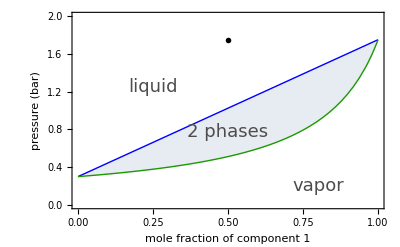
-Graphics-
Figure 1

```mathematica
Framed@Column[{
Framed@Module[{Px,Py,Psat1,Psat2},
Psat1=1.75;
Psat2=0.3;
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
Show[
Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},PlotRange->{{0,1},{0,2.}},Frame->True,Background->White,FrameLabel->{Style["mole fraction of component 1",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial",13},ImageSize->400,Filling->{1->{{2},Opacity[0.1,Blend[{Blue,RGBColor[0.1,0.6,0]},0.5]]}},
Epilog->
Inset[
(*Framed[*)Graphics[{
{Thick,RGBColor[0.1,0.6,0],Line[{{0,0},{1,0}}]},
Text[Style["dew",17,FontFamily->"Arial"],{1.85,0}],
{Thick,Blue,Line[{{3.5,0},{4.5,0}}]},
Text[Style["bubble",17,FontFamily->"Arial"],{5.75,0}]
},ImageSize->{175,25},PlotRange->{{0,6.75},{-0.25,0.25}}](*,FrameMargins->Tiny]*),{0.5,1.75}]
],
Graphics[{
Text[Style["liquid",18,FontFamily->"Arial",GrayLevel[0.3]],{0.25,1.25}],
Text[Style["vapor",18,FontFamily->"Arial",GrayLevel[0.3]],{0.8,0.2}],
Text[Style["2 phases",18,FontFamily->"Arial",GrayLevel[0.3]],{0.5,0.5*(Px[0.5]+Py[0.5])}]
}]
]
],
Text@Style["Figure 1",16,Bold,FontFamily->"Arial",Darker[Cyan,0.65]]},Alignment->Center]
```

## Lever Rule

The relative amounts of liquid and vapor for any point in the two-phase region can be calculated using the lever rule. An derivation of the lever rule is given in the screencast  xxxxxx (need one that uses Pxy diagram). The equations below are for a basis on one mole:

liquid amount present at z:     L=(z_1-y_1)/(x_1-y_1)

vapor amount present at z:      V=(z_1-x_1)/(y_1-x_1)

Mouseover Figure 2 to see what points are used in the lever rule calculation.

```mathematica
Framed[Column[{
Framed@Module[{p,Psat1,Psat2,Px,Py,x1,y1,leverx,levery,p1,p2,p3},
p=0.733;
(*Psat1=1.569; *)
Psat1=1.536;
Psat2=0.319; 
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x1=X/.FindRoot[p==X*Psat1+(1-X)*Psat2,{X,0}];
y1=Y/.FindRoot[p==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
leverx=Which[
x1<0.4<y1,(y1-0.4)/(y1-x1),
Px[0.4]≤p,1,
Py[0.4]≥p,0];
levery=1-leverx;
p1=Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},Frame->True,PlotRange->{{0,1},{0.3,1.6}},FrameLabel->{Style["mole fraction of component 1",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial",13},ImageSize->400,
Epilog->Inset[Graphics[{PointSize[0.05],Point[{0,0}]}],{0.4,p}]];
p2=Graphics[{
{Thick,Dashed,Blue,Line[{{x1,p},{0.4,p}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.4,p},{y1,p}}]},
{Thickness[0.005],Line[{{x1,p},{x1,p+0.04},{0.39,p+0.04},{0.39,p}}]},{Thickness[0.005],Line[{{(x1+0.4)/2,p+0.04},{(x1+0.4)/2,p+0.4}}]},
{Thickness[0.005],Line[{{0.41,p},{0.41,p+0.04},{y1,p+0.04},{y1,p}}]},{Thickness[0.005],Line[{{(0.4+y1)/2,p+0.04},{(0.4+y1)/2,p+0.4}}]},
Text[Style[Column[{Row[{NumberForm[leverx*100,2],"%"}],"liquid"},Alignment->Center],17,FontFamily->"Arial"],{(y1+0.4)/2,p+0.52}],
Text[Style[Column[{Row[{NumberForm[levery*100,2],"%"}],"vapor"},Alignment->Center],17,FontFamily->"Arial"],{(x1+0.4)/2,p+0.52}]
}];
p3=Graphics[{
{Thick,Dashed,Blue,Line[{{x1,p},{0.4,p}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.4,p},{y1,p}}]},
{Thickness[0.005],Line[{{x1,p},{x1,p+0.04},{0.39,p+0.04},{0.39,p}}]},{Thickness[0.005],Line[{{(x1+0.4)/2,p+0.04},{(x1+0.4)/2,p+0.4}}]},
{Thickness[0.005],Line[{{0.41,p},{0.41,p+0.04},{y1,p+0.04},{y1,p}}]},{Thickness[0.005],Line[{{(0.4+y1)/2,p+0.04},{(0.4+y1)/2,p+0.4}}]},
Text[Style["L",17,FontFamily->"Arial"],{(y1+0.4)/2,p+0.45}],
Text[Style["V",17,FontFamily->"Arial"],{(x1+0.4)/2,p+0.45}],
{PointSize[0.015],Point[{x1,p}]},Text[Style["x_1",17,FontFamily->"Arial"],{x1,p},{-1,1}],
{PointSize[0.015],Point[{0.4,p}]},Text[Style["z_1",17,FontFamily->"Arial"],{0.415,p},{-1,1}],
{PointSize[0.015],Point[{y1,p}]},Text[Style["y_1",17,FontFamily->"Arial"],{y1,p},{-1,1}]
}];
Mouseover[Show[p1,p2,Background->White],Show[p1,p3,Background->White]]
],
Text@Style["Figure 2",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center]]
```

Figure 2

Test Yourself

For the system in Figure 2, use the lever rule to calculate the fraction of liquid and vapor present for an overall molar composition z_1=0.6 and a pressure of 0.7 bar. Note that at 0.7 bar, x_1=0.31 and y_1=0.69.

#### Solution

The fraction of liquid present is,
 
	L=(z_1-y_1)/(x_1-y_1)=(0.6-0.69)/(0.31-0.69)=0.23   or  23%   liquid
	
The fraction of vapor present  is,
 
	V=(z_1-x_1)/(y_1-x_1)=(0.6-0.31)/(0.69-0.31)=0.77   or  77%  vapor

Use the Demonstration below to see how the amount of liquid and vapor present changes with overall composition (Figure 3).

```mathematica
Framed[Column[{Manipulate[
Module[{p,Psat1,Psat2,Px,Py,x1,y1,leverx,levery},
p=0.7;
Psat1=1.536; 
Psat2=0.319;
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x1=X/.FindRoot[p==X*Psat1+(1-X)*Psat2,{X,0}];
y1=Y/.FindRoot[p==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
leverx=Which[
x1<comp<y1,(y1-comp)/(y1-x1),
Px[comp]≤p,1,
Py[comp]≥p,0];
levery=1-leverx;
Show[
Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},PlotRange->{{0,1},{0.,1.75}},Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial",13},AxesOrigin->{0,100},ImageSize->400],
Graphics[{
{Thick,Dashed,Blue,Line[{{x1,p},{comp,p}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{comp,p},{y1,p}}]},
If[comp>0.33,{Thickness[0.0045],Line[{{x1,p},{x1,p+0.04},{comp-0.01,p+0.04},{comp-0.01,p}}]}],{Thickness[0.0045],Line[{{(x1+comp)/2,p+0.04},{(x1+comp)/2,p+0.4}}]},
If[comp<0.71,{Thickness[0.0045],Line[{{comp+0.01,p},{comp+0.01,p+0.04},{y1,p+0.04},{y1,p}}]}],{Thickness[0.0045],Line[{{(comp+y1)/2,p+0.04},{(comp+y1)/2,p+0.4}}]},
Text[Style[Column[{Row[{NumberForm[leverx*100,2],"%"}],"liquid"},Alignment->Center],17,FontFamily->"Arial",Background->White],{(y1+comp)/2,p+0.55}],
Text[Style[Column[{Row[{NumberForm[levery*100,2],"%"}],"vapor"},Alignment->Center],17,FontFamily->"Arial"],{(x1+comp)/2,p+0.55}],

Line[{{0.5*(y1+comp),p-0.01},{0.5*(y1+comp)+0.05,0.25}}],Line[{{0.5*(x1+comp),p-0.01},{0.5*(x1+comp)-0.05,0.25}}],

Text[Framed[Style["L/(L + V)",16],Background->White],{0.5*(y1+comp)+0.05,0.25}],
Text[Framed[Style["V/(L + V)",16],Background->White],{0.5*(x1+comp)-0.05,0.25}],

{PointSize[0.02],Point[{comp,p}]},
Text[Style["liquid",18,FontFamily->"Arial",GrayLevel[0.3]],{0.15,1.55}],
Text[Style["vapor",18,FontFamily->"Arial",GrayLevel[0.3]],{0.9,0.2}]
}]
]
],
{{comp,0.6,Style["overall molar composition (z_1)",13,FontFamily->"Arial"]},0.3,0.69,0.01,Appearance->"Labeled"}],
Text@Style["Figure 3",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 3

## Pressure Dependence

### Effect on Lever Rule Amounts

Move the pressure slider in Figure 4 and observe how the amounts of liquid and vapor change (bar graph) at a constant overall composition of 0.5. Note how the composition of component 1 in each phase changes as the pressure changes.

```mathematica
Framed[Column[{Manipulate[
Module[{Psat1,Psat2,Px,Py,x1,y1,leverx,levery,p1,p2,p3},
Psat1=1.536;
Psat2=0.319;
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x1=X/.FindRoot[p==X*Psat1+(1-X)*Psat2,{X,0}];
y1=Y/.FindRoot[p==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
leverx=Which[
x1<0.5<y1,(y1-0.5)/(y1-x1),
Px[0.5]≤p,1,
Py[0.5]≥p,0];
levery=1-leverx;
p1=Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},PlotRange->{{0,1},{0.3,1.6}},Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial",13},ImageSize->400,
Epilog->Inset[Graphics[{PointSize[0.09],Point[{0,0}]}],{0.5,p}]];
p2=BarChart[{leverx,levery},ChartStyle->{Blue,RGBColor[0.1,0.6,0]},ChartLayout->"Stacked",AspectRatio->Full,ImageSize->{100,250},ChartLabels->Placed[{Framed[Style[Row[{NumberForm[100*leverx,{3,0}]," % L"}],15,FontFamily->"Arial",Bold],Background->White],Framed[Style[Row[{NumberForm[100*levery,{3,0}]," % V"}],15,FontFamily->"Arial",Bold],Background->White]},Center],LabelStyle->{Black,FontFamily->"Arial",13}];
p3=Graphics[{
If[leverx==1∨levery==1,Text[""],
{{Thick,Dashed,Blue,Line[{{x1,p},{0.5,p}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.5,p},{y1,p}}]}}]
}];
Row[{Show[p1,p3],Spacer[10],Show[p2]}]
],
{{p,0.7,Style["pressure (bar)",13,FontFamily->"Arial"]},0.4,1.25,0.05,Appearance->"Labeled"}],
Text@Style["Figure 4",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 4

### Effect on Molar Composition

Test Yourself

A piston-cylinder system (Figure 5) contains components A and B in VLE. Assume the system is ideal, with x_A=0.25 and y_A=0.5. A small weight is added to the piston at constant temperature. What happens as pressure increases?

A. x_A increases, y_A decreases

Incorrect.

B. x_A increases, increases

Correct. Use the slider in Figure 6 to increase the pressure and see what effect it has on x_A and y_A.

B. x_A increases, increases

Correct. Use the slider in Figure 6 to increase the pressure and see x_A and y_A increase.

```mathematica
Framed[Column[{Manipulate[
Module[{Psat1,Psat2,Px,Py,x0,y0,x1,y1,leverx,levery,p1,p2},
Psat1=1.536;
Psat2=0.319;
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x0=X/.FindRoot[0.7==X*Psat1+(1-X)*Psat2,{X,0}];
y0=Y/.FindRoot[0.7==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
x1=X/.FindRoot[p==X*Psat1+(1-X)*Psat2,{X,0}];
y1=Y/.FindRoot[p==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
leverx=Which[
x1<0.5<y1,(y1-0.5)/(y1-x1),
Px[0.5]≤p,1,
Py[0.5]≥p,0];
levery=1-leverx;
p1=Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},PlotRange->{{0,1},{0.1,1.6}},Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial",13},ImageSize->400];

p2=Graphics[{
{Thick,Dashed,Blend[{Blue,Gray},0.65],Line[{{x0,0.7},{0.5,0.7}}]},
{Thick,Dashed,Blend[{RGBColor[0.1,0.6,0],Gray},0.65],Line[{{0.5,0.7},{y0,0.7}}]},
{Thick,Dashed,Blend[{Blue,Gray},0.65],Line[{{x0,0.7},{x0,0.1}}]},
{Thick,Dashed,Blend[{RGBColor[0.1,0.6,0],Gray},0.65],Line[{{y0,0.7},{y0,0.1}}]},
{Gray,PointSize[0.02],Point[{0.5,0.7}]},

{Thick,Dashed,Blue,Line[{{x1,p},{0.5,p}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.5,p},{y1,p}}]},
{Thick,Dashed,Blue,Line[{{x1,p},{x1,0.133}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{y1,p},{y1,0.133}}]},
{PointSize[0.02],Point[{0.5,p}]},
If[p==0.7,Text@"",{{Thick,Arrow[{{x0,0.2},{x1,0.2}}]},{Thick,Arrow[{{y0,0.2},{y1,0.2}}]}}]
}];
Show[p1,p2]
],{{p,0.7,Style["pressure (bar)",13,FontFamily->"Arial"]},0.55,0.9,0.01,Appearance->"Labeled"}],
Text@Style["Figure 6",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 6

C. x_A decreases, decreases

Incorrect.

D. x_A decreases, y_A increases

Incorrect.

```mathematica
Framed@Column[{
Framed@Graphics[Inset[Graphics3D[{
{Opacity[0.3],Cylinder[{{0,0,0},{0,0,2}},0.75]},
{Gray,Cylinder[{{0,0,1.5},{0,0,1.75}},0.75]},
{RGBColor[0.,0.65,0.9],Cylinder[{{0,0,0},{0,0,0.55}},0.75]},
{FaceForm[Black],Cuboid[{-0.25,0,2.25},{0.25,0,2.65}]},
{Thickness[0.02],Arrowheads[0.05],Arrow[{{0,0,2.25},{0,0,1.85}}]},
Text[Style[Column[{"vapor","y_A = 0.5"},Alignment->Center],18,FontFamily->"Arial"],{0,0,1.}],
Text[Style[Column[{"liquid","x_A = 0.25"},Alignment->Center],18,FontFamily->"Arial"],{0,0,0.15}]
},Boxed->False,ViewPoint->Front,Lighting->{{"Ambient",LightGray}},Background->White,ImageSize->150]],ImageSize->{150,264},PlotRange->{{-1,1},{-0.75,2.75}}],
Text@Style["Figure 5",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center]
```

-Graphics-
Figure 5

Screencasts that describe system in more detail: Increase Pressure on Binary VLE System (Interactive) and Pressure Effect on VLE

Test Yourself

A 50/50 mol% liquid mixture of n-pentane and n-heptane is at pressure of 1.2 bar in Figure 7. The pressure is lowered isothermally until the mixture begins to vaporize at about 0.95 bar. P_P^sat>P_H^sat. Which statement is true?

A. n-Heptane is enriched in the vapor phase

Incorrect.

B. n-Pentane is enriched in the vapor phase

Correct. n-Pentane is the more volatile component so it will be enriched in the vapor phase.

C. The composition in the vapor phase is 50/50 mol%

Incorrect.

D. The mixture does not vaporize

Incorrect.

```mathematica
Framed[Column[{
Manipulate[
Module[{Psat1,Psat2,Px,Py,x1,y1,leverL,leverV},
Psat1=1.536;
Psat2=0.319;
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x1=x/.FindRoot[x*Psat1+(1-x)*Psat2==P,{x,0.4}];
y1=x/.FindRoot[(x/Psat1+(1-x)/Psat2)^-1==P,{x,0.5}];
leverL=If[P<Px[0.5],(0.5-y1)/(x1-y1),1];
leverV=1-leverL;
Show[
Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},Frame->True,FrameLabel->{Style[Row[{"mole fraction of ",Style["n",Italic],"-pentane"}],17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial",13},PlotRange->{{0,1},{0.1,1.6}},ImageSize->400,
Epilog->Inset[Graphics[{PointSize[0.045],Point[{0,0}]}],{0.5,P}]],
If[P<Px[0.5],
Graphics[{
{Thick,Blue,Dashed,Line[{{x1,P},{0.5,P}}]},
{Thick,Blue,Dashed,Line[{{x1,P},{x1,0.1}}]},
{Thick,RGBColor[0.1,0.6,0],Dashed,Line[{{0.5,P},{y1,P}}]},
{Thick,RGBColor[0.1,0.6,0],Dashed,Line[{{y1,P},{y1,0.1}}]},
Text[Framed[Style[Row[{"x = ",NumberForm[x1,2]}],17,FontFamily->"Arial"],Background->LightGray],{x1,0.65*P}],
Text[Framed[Style[Row[{"y = ",NumberForm[y1,2]}],17,FontFamily->"Arial"],Background->LightGray],{y1,0.65*P}],

{Thickness[0.0035],Line[{{0.5*(x1+0.5)-0.05,1},{0.5*(x1+0.5),P}}]},
{Thickness[0.0035],Line[{{0.5*(y1+0.5)+0.05,1},{0.5*(y1+0.5),P}}]},
Text[Framed[Style[Row[{NumberForm[100*leverL,2],"% L"}],17,FontFamily->"Arial"],Background->LightGray],{0.5*(y1+0.5)+0.05,1}],
Text[Framed[Style[Row[{NumberForm[100*leverV,2],"% V"}],17,FontFamily->"Arial"],Background->LightGray],{0.5*(x1+0.5)-0.05,1}]
}],
Graphics[{
{Thickness[0.0035],Line[{{0.35,1.4},{0.5,P}}]},
Text[Framed[Style["50/50 mol%",17,FontFamily->"Arial"],Background->LightGray],{0.35,1.4}]
}]
]]
],
{{P,1.2,Style["press the play button for pressure to decrease",13,FontFamily->"Arial"]},1.2,0.7,Trigger,AnimationRate->10,AppearanceElements->{"PlayPauseButton","ResetButton"}}],
Text@Style["Figure 7",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 7

## Temperature Dependence

How will the curves in the P-x-y diagram in (Figure 8) shift as temperature changes?

```mathematica
Framed[Column[{Manipulate[
Module[{Psat1,Psat2,T0,Px0,Py0,Px,Py,p0,p1},
Psat1=0.00133322368*10^(6.90565-1211.033/(T+220.79)); 
Psat2=0.00133322368*10^(6.65464-1344.8/(T+219.48)); 
T0=110;
Px0[x_]=x*0.00133322368*10^(6.90565-1211.033/(T0+220.79))+(1-x)*0.00133322368*10^(6.65464-1344.8/(T0+219.48));
Py0[x_]=(x/(0.00133322368*10^(6.90565-1211.033/(T0+220.79)))+(1-x)/(0.00133322368*10^(6.65464-1344.8/(T0+219.48))))^-1;
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
Plot[{Px[x],Py[x],Px0[x],Py0[x]},{x,0,1},
PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]},If[T==110,None,{Thick,Dashed,Blend[{Blue,Gray},0.5]}],If[T==110,None,{Thick,Dashed,Blend[{RGBColor[0.1,0.6,0],Gray},0.5]}]},PlotRange->{{0,1},{0.1,3}},Frame->True,
FrameLabel->{Style["mole fraction of component 1",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial",13},LabelStyle->FontSize->16,ImageSize->400]
],
{{T,110,Style["temperature (°C)",13,FontFamily->"Arial"]},95,120,1,Appearance->"Labeled"}],
Text@Style["Figure 8",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 8

Test Yourself

For a 50/50 mol% mixture (z=0.5) in VLE at 1.2 bar in Figure 9, will the amount of liquid in the system increase or decrease when the temperature increases?

#### Solution

The amount of liquid present will decrease, subsequently the amount of vapor increases. Move the temperature slider in Figure 9 to see how the amount of liquid and vapor phases change. A different pressure can also be chosen.

```mathematica
Framed[Column[{Manipulate[
Module[{Psat1,Psat2,Px,Py,x1,y1,leverx,levery,p1,p2,p3},
Psat1=0.00133322368*10^(6.90565-1211.033/(T+220.79)); 
Psat2=0.00133322368*10^(6.65464-1344.8/(T+219.48)); 
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x1=X/.FindRoot[P==X*Psat1+(1-X)*Psat2,{X,0}];
y1=Y/.FindRoot[P==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
leverx=Which[
x1<0.5<y1,(y1-0.5)/(y1-x1),
Px[0.5]≤P,1,
Py[0.5]≥P,0];
levery=1-leverx;
p1=Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["pressure (bar)",17]},PlotRange->{{0,1},{0.1,3}},LabelStyle->{Black,FontFamily->"Arial",13},LabelStyle->FontSize->16,ImageSize->400,
Epilog->Inset[Graphics[{PointSize[0.085],Point[{0,0}]}],{0.5,P}]
];
p2=BarChart[{leverx,levery},ChartStyle->{Blue,RGBColor[0.1,0.6,0]},ChartLayout->"Stacked",AspectRatio->Full,ImageSize->{100,250},ChartLabels->Placed[{Framed[Style[Row[{NumberForm[100*leverx,{3,0}]," % L"}],15,FontFamily->"Arial",Bold],Background->White],Framed[Style[Row[{NumberForm[100*levery,{3,0}]," % V"}],15,FontFamily->"Arial",Bold],Background->White]},Center],LabelStyle->{Black,FontFamily->"Arial",13}];
p3=Graphics[{
If[leverx==1∨levery==1,Text[""],
{{Thick,Dashed,Blue,Line[{{x1,P},{0.5,P}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.5,P},{y1,P}}]}}]
}];
Row[{Show[p1,p3],Spacer[10],Show[p2]}]
],
{{T,110,Style["temperature (°C)",13,FontFamily->"Arial"]},95,120,1,Appearance->"Labeled"},
{{P,1.2,Style["pressure (bar)",13,FontFamily->"Arial"]},0.5,2,0.1,Appearance->"Labeled"}],
Text@Style["Figure 9",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 9

Test Yourself

When the temperature of a 50/50 vapor mixture of benzene and toluene is lowered, the technician observes that toluene condenses before benzene. Is this possible?

Hint

Consider Raoult’s law and refer to the simulation in Figure 9.

A. Yes, if benzene has a lower vapor pressure than toluene

Incorrect.

B. Yes, if benzene has a higher vapor pressure than toluene

Incorrect.

C. No, both species have to condense

Correct. Since these two components are miscible, both will condense (Figure 10).

```mathematica
Framed[Column[{
Manipulate[
Module[{Psat1,Psat2,Px,Py,P,x1,y1},
Psat1=10^(4.6-1701/(T+293.8));
Psat2=10^(4.1-1344/(T+219.2));
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
P=0.83;
x1=X/.Quiet@FindRoot[Px[X]==P,{X,0.1}];
y1=Y/.Quiet@FindRoot[Py[Y]==P,{Y,0.1}];
Show[
Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}}],
Graphics[{
If[Py[0.5]≤P,
{Text[Style["liquid forms",18,FontFamily->"Arial",GrayLevel[0.5]],{0.5,1.5}],
Text[Framed@Style[Column[{Row[{"x_B = ",NumberForm[x1,2]}],Row[{"x_T = ",NumberForm[1-x1,2]}]},Alignment->"="],15,FontFamily->"Arial"],{0.27,0.87},{1,-1}],
Text[Framed[Style[Column[{Row[{"y_B = ",NumberForm[y1,2]}],Row[{"y_T = ",NumberForm[1-y1,2]}]},Alignment->"="],15,FontFamily->"Arial"],Background->White],{0.54,0.79},{-1,1}],
{Thick,Dashed,{Blue,Line[{{x1,0},{x1,P},{0.5,P}}]},{RGBColor[0.1,0.6,0],Line[{{0.5,P},{y1,P},{y1,0}}]}}
},
{Text[Framed[Style[Column[{"y_B = 0.5","y_T = 0.5"},Alignment->"="],15,FontFamily->"Arial"],Background->White],{0.54,0.79},{-1,1}],
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.5,P},{0.5,0}}]}
}],
{PointSize[0.02],Point[{0.5,P}]}
}],
Frame->True,FrameLabel->{Style["mole fraction of benzene",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial",13},ImageSize->400,Axes->False,PlotRange->{{0,1},{0.5,1.9}}]
],
Style["lower temperature to see benzene and toluene condense:",13,FontFamily->"Arial"],
{{T,100,Style["temperature (°C)",13,FontFamily->"Arial"]},100,90,1,Appearance->"Labeled"}
],Text@Style["Figure 10",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 10

D. It depends on the system pressure as to whether one or two species condense.

Incorrect.

Test Yourself

Initially, 20.1 mol of n-hexane is in VLE. What happens when 2 mol n-octane are added? Note that n-hexane has a higher saturation pressure than n-octane. Move the mouse over Figure 11 to view the P-x-y diagram. Once you have selected an answer, click “inject isothermally.”

A. All condense

Correct. Since only n-hexane in VLE was present initially, the addition of n-octane (less volatile) will result in all components condensing (see Figure 11).

B. All vaporize

Incorrect.

C. A vapor-liquid mixture forms

Incorrect.

```mathematica
Framed[Column[{Manipulate[
Module[{PsatH,PsatO,amtL,step,pto,h,f,piston,zi,tank,plotPxy},
PsatH=0.247474;
PsatO=0.024569;
zi=0.0905;
amtL=If[cs==1,0.182+0.02*step,0.182*(1-step)];

step=If[cs==1,amt1,amt2];

pto={0,0,0};
h=2.75;
f=Sequence[FontSize->18,FontFamily->"Arial"];

piston=2.35+(amtL*h-2.35)*step;

tank=Graphics[
Inset[
Graphics3D[{
{Opacity[0.5],Cylinder[{pto,{0,0,h}}],Cylinder[{{1,0,h/2},{2,0,h/2}},0.13]},
{Opacity[0.75],RGBColor[0.07,1,0.6],Cylinder[{pto,{0,0,amtL*h}}],Cylinder[{{1,0,h/2},{1+0.4*(1-step),0,h/2}},0.13]},
Cylinder[{{1+0.4*(1-step),0,h/2},{2.05+0.4*(1-step),0,h/2}},0.04],
{Black,Cylinder[{{2.05+0.4*(1-step),0,h/2},{2.075+0.4*(1-step),0,h/2}},0.14]},

{Gray,If[cs==1,
{Cylinder[{{0,0,piston},{0,0,2.5-2.35+piston}}],
Cylinder[{{0,0,2.5-2.35+piston},{0,0,2.85}},0.1]},
{Cylinder[{{0,0,2.35+0.25*step},{0,0,2.5+0.25*step}}],
Cylinder[{{0,0,2.5+0.25*step},{0,0,2.85}},0.1]
}]},

If[cs==1,{
Text[Style[If[amt1==1,"all vapor condenses",""],Evaluate@f],{2.2,0,1.75}],
Text[Style[If[amt1==1,
Row[{"2 mol ",Style["n",Italic],"-octane added"}],
Row[{"add 2 mol ",Style["n",Italic],"-octane"}]],Evaluate@f],{2.2,0,1}],
Text[Style[If[step≥0.8,"",
Column[{Row[{"0.1 mol ",Style["n",Italic],"-hexane"}],"vapor"},Alignment->Center]],Evaluate@f],{0,0,0.5*piston+(0.55*amtL*h-0.5*piston)*step}],
Text[Style[If[amt1==1,
Row[{"20.1 mol ",Style["n",Italic],"-hexane"}],
Column[{Row[{"20 mol ",Style["n",Italic],"-hexane"}],"liquid"},Alignment->Center]],Evaluate@f],{0,0,(0.15+0.45*step)*amtL*h}],
Text[Style[If[amt1==1,Row[{"2 mol ",Style["n",Italic],"-octane"}],""],Evaluate@f],{0,0,0.1*amtL*h}]},

{Text[Style[If[amt2==1,"all liquid evaporates",""],Evaluate@f],{2.2,0,1.75}],
Text[Style[If[amt2==1,
Row[{"2 mol ",Style["n",Italic],"-hexane added"}],
Row[{"add 2 mol ",Style["n",Italic],"-hexane"}]],Evaluate@f],{2.2,0,1}],
Text[Style[If[amt2==1,
Row[{"20.1 mol ",Style["n",Italic],"-octane"}],
Column[{Row[{"0.1 mol ",Style["n",Italic],"-octane"}],"vapor"},Alignment->Center]],Evaluate@f],{0,0,If[amt2<1,0.5*2.35,h/2]}],
If[amt2==1,
Text[Style[Row[{"2 mol ",Style["n",Italic],"-hexane"}],Evaluate@f],{0,0,0.45*2.35}],
Text[Style[Column[{Row[{"20 mol ",Style["n",Italic],"-octane"}],"liquid"},Alignment->Center],Evaluate@f],{0,0,0.15*amtL*h*(1-step)}]
]
}]
},
Lighting->{{"Ambient",LightGray}},Boxed->False,ViewPoint->Front,PlotRange->{{-1,3.25},{-1,1},{0,3}},ImageSize->400]
],PlotRange->{{-1,3.25},{0,3}},ImageSize->400];

plotPxy=Show[
Plot[{x*PsatH+(1-x)*PsatO,(x/PsatH+(1-x)/PsatO)^-1},{x,0,1},
Frame->True,FrameLabel->{Style[Row[{Style["n",Italic],"-hexane mole fraction"}],16],Style["pressure (bar)",16]},
LabelStyle->{Black,FontFamily->"Arial",13},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},ImageSize->{400,282}],
Graphics[{
If[cs==1,
Text[Style[If[amt1==1,"all liquid",""],18,GrayLevel[0.4],FontFamily->"Arial"],{0.2,0.2}],
Text[Style[If[amt2==1,"all vapor",""],18,GrayLevel[0.4],FontFamily->"Arial"],{0.8,0.025}]],
If[cs==1,
{{Thickness[0.0055],Dashed,Line[{{1-zi*step,PsatH},{1,PsatH}}]},
{PointSize[0.02],Point[{1-zi*step,PsatH}]}},
{{Thickness[0.0055],Dashed,Line[{{0,PsatO},{zi*step,PsatO}}]},
{PointSize[0.02],Point[{zi*step,PsatO}]}}]
}]
];
Mouseover[
Show[tank],Show[plotPxy]
]
],
Control[{{cs,1,Style["component to inject",13,FontFamily->"Arial"]},{1->Style[Row[{Style["n",Italic],"-octane"}],13,FontFamily->"Arial"],2->Style[Row[{Style["n",Italic],"-hexane"}],13,FontFamily->"Arial"]},Setter}],
PaneSelector[{
1->Control[{{amt1,0,Style["inject isothermally",13,FontFamily->"Arial"]},0,1,Trigger,AnimationRate->1,AppearanceElements->{"PlayPauseButton","ResetButton"}}],
2->Control[{{amt2,0,Style["inject isothermally",13,FontFamily->"Arial"]},0,1,Trigger,AnimationRate->1,AppearanceElements->{"PlayPauseButton","ResetButton"}}]
},Dynamic@cs]
],Text@Style["Figure 11",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 11

Suppose instead that the more volatile component, n-hexane, were added to n-octane in VLE. Will the final state be all vapor? All liquid? Or a vapor-liquid mixture? In Figure 11, select “add n-hexane” and press the play button to see what happens.

## Temperature-Composition (T-x-y) Diagrams

## Raoult’s Law

A temperature-composition (T-x-y) diagram at constant pressure can also be used to demonstrate vapor-liquid equilibrium. For a given temperature and constant pressure, molar compositions in the liquid and vapor phases can be calculated using Raoult’s law.

For a pressure of 1.5 bar and 125 °C, calculate the liquid (x_1) and vapor (y_1) mole fractions using Raoult’s law. Note that P_1^sat=3.47 bar and P_2^sat=0.69 bar at 125 °C.

#### Solution

Recall the total pressure is equal to the sum of the partial pressures:

P=x_1 P_1^sat+x_2 P_1^sat

1.5 bar=x_1 (3.47)+(1-x_1) (0.69)

x_1=0.23

x_2=0.77

Raoult’s law states:

x_1 P_1^sat=y_1 P  or

y_1=(x_1 P_1^sat)/P

y_1=((0.23) (3.47 bar))/(1.5 bar)

y_1=0.6

y_2=0.4

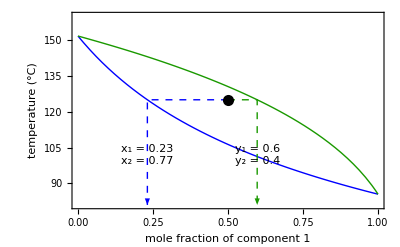
-Graphics-
Figure 12

```mathematica
Framed@Column[{Framed@Module[{Tx,Ty,x1,y1},
Tx=Interpolation[{{0.,151.67026635493596},{0.05,144.5109287606565},{0.1,138.2643918873679},{0.15000000000000002,132.7467925644698},{0.2,127.82249462360052},{0.25,123.3889121440843},{0.30000000000000004,119.36680832863544},{0.35000000000000003,115.69386968427179},{0.4,112.32032035499262},{0.45,109.20585126140715},{0.5,106.31742161257496},{0.55,103.62765402156094},{0.6000000000000001,101.11364257052611},{0.65,98.75605383230217},{0.7000000000000001,96.53843938921682},{0.75,94.44670346145526},{0.8,92.4686859222792},{0.8500000000000001,90.59383226887708},{0.9,88.81292990604823},{0.9500000000000001,87.11789555186844},{1.,85.50160245324302}}];
Ty=Interpolation[{{0.,151.67026635493596},{0.19389786615463564,144.5109287606565},{0.34183285093948057,138.2643918873679},{0.4572890121992593,132.7467925644698},{0.5491304056795199,127.82249462360052},{0.6233822087386978,123.3889121440843},{0.6842579993508155,119.36680832863544},{0.7347774869026447,115.69386968427179},{0.777151428363227,112.32032035499262},{0.8130289737113512,109.20585126140715},{0.8436609487807419,106.31742161257496},{0.8700102403984356,103.62765402156094},{0.8928280185640353,101.11364257052611},{0.9127073779702445,98.75605383230217},{0.9301217406488608,96.53843938921682},{0.9454527793523965,94.44670346145526},{0.9590110106582255,92.4686859222792},{0.971051180031471,90.59383226887708},{0.9817838935292167,88.81292990604823},{0.9913845087381005,87.11789555186844},{0.9999999999999961,85.50160245324302}}];
x1=x/.FindRoot[Tx[x]==125,{x,0.1}];
y1=y/.FindRoot[Ty[y]==125,{y,0.1}];
Show[
Plot[{Tx[x],Ty[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["temperature (°C)",17]},LabelStyle->{FontFamily->"Arial",Black,13},ImageSize->400,PlotRange->{{0,1},{81,160}}],
Graphics[{
{Thick,Dashed,
{Arrowheads[0.05],Blue,Arrow[{{0.5,125},{x1,125},{x1,81}}]},
{Arrowheads[0.05],RGBColor[0.1,0.6,0],Arrow[{{0.5,125},{y1,125},{y1,81}}]}},
{PointSize[0.02],Point[{0.5,125}]},
Text[Framed[Style[Column[{"x_1 = 0.23","x_2 = 0.77"}],16,FontFamily->"Arial"],Background->White],{x1,102}],
Text[Framed[Style[Column[{"y_1 = 0.6","y_2 = 0.4"}],16,FontFamily->"Arial"],Background->White],{y1,102}]
}]]
],Text@Style["Figure 12",16,Bold,FontFamily->"Arial",Darker[Cyan,0.65]]},Alignment->Center]
```

The screencast Bubble Temperature: Raoult’s Law shows an example of solving for the bubble temperature.

The T-x-y diagram in Figure 13 is at constant pressure. As temperature is lowered below the dew point, the mixture starts to condense. Likewise, as the temperature is raised above the bubble point, the liquid starts to vaporize. The shaded region represents the 2-phase region. Note that for P_1^sat>P_2^sat (the condition for the P-x-y diagrams), T_1^sat<T_2^sat, as shown in Figure 13.

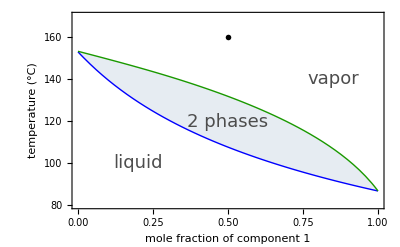
-Graphics-
Figure 13

```mathematica
Framed@Column[{Framed@Module[{Tx,Ty},
Tx=Interpolation[{{0.05,145.8451408873339},{0.1,139.58547026975},{0.15000000000000002,134.05492689988247},{0.2,129.11797224761773},{0.25,124.6720835080173},{0.30000000000000004,120.63806121044892},{0.35000000000000003,116.9536106942855},{0.4,113.56896202995672},{0.45,110.4438032691518},{0.5,107.54508491468462},{0.55,104.84541713633303},{0.6000000000000001,102.32187931270607},{0.65,99.95512208205086},{0.7000000000000001,97.728680571184},{0.75,95.6284425073631},{0.8,93.64223155677921},{0.8500000000000001,91.75947750505516},{0.9,89.97095267131337},{0.9500000000000001,88.26855938818143},{1.,86.64515725298341}}];
Ty=Interpolation[{{0.19317811721854555,145.8451408873339},{0.3407321042975589,139.58547026975},{0.4560091592266281,134.05492689988247},{0.5477931523209137,129.11797224761773},{0.6220610267814846,124.6720835080173},{0.6829967401451854,120.63806121044892},{0.7336015275972564,116.9536106942855},{0.7760745025654346,113.56896202995672},{0.8120574390943044,110.4438032691518},{0.8427964960797252,107.54508491468462},{0.8692516349842526,104.84541713633303},{0.8921722307928908,102.32187931270607},{0.91215032141785,99.95512208205086},{0.9296587555026532,97.728680571184},{0.9450789483764741,95.6284425073631},{0.9587213642068871,93.64223155677921},{0.9708408270488005,91.75947750505516},{0.9816481029842187,89.97095267131337},{0.991318757809891,88.26855938818143},{0.9999999999999899,86.64515725298341}}];

Quiet@Show[
Plot[{Tx[x],Ty[x]},{x,0,1},
PlotRange->{{0,1},{80,170}},ImageSize->400,Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["temperature (°C)",17]},
LabelStyle->{FontFamily->"Arial",Black,13},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},
Filling->{1->{{2},Opacity[0.1,Blend[{Blue,RGBColor[0.1,0.6,0]},0.5]]}},
Epilog->
Inset[
Graphics[{
{Thick,RGBColor[0.1,0.6,0],Line[{{0,0},{1,0}}]},
Text[Style["dew",17,FontFamily->"Arial"],{1.85,0}],
{Thick,Blue,Line[{{3.5,0},{4.5,0}}]},
Text[Style["bubble",17,FontFamily->"Arial"],{5.75,0}]
},ImageSize->{175,25},PlotRange->{{0,6.75},{-0.25,0.25}}],{0.5,160}]
],
Graphics[{
Text[Style["liquid",18,FontFamily->"Arial",GrayLevel[0.3]],{0.2,100}],
Text[Style["vapor",18,FontFamily->"Arial",GrayLevel[0.3]],{0.85,140}],
Text[Style["2 phases",18,FontFamily->"Arial",GrayLevel[0.3]],{0.5,0.5*(Tx[0.5]+Ty[0.5])}]
}]
]
],Text@Style["Figure 13",16,Bold,FontFamily->"Arial",Darker[Cyan,0.65]]},Alignment->Center]
```

## Temperature Dependence

For an ideal mixture at constant overall composition (z_1=0.5) use the demonstrations below to see how varying temperature affects the amount of liquid and vapor present and the molar compositions of each phase.

As temperature is increased, the mixture vaporizes (Figure 14). Recall from the previous section, if the pressure is raised the mixture is compressed and condenses.

```mathematica
Framed[Column[{Manipulate[Module[{Tx,Ty,x1,y1,leverL,leverV,p1,p2},
Tx=Interpolation[{{0.05,145.8451408873339},{0.1,139.58547026975},{0.15000000000000002,134.05492689988247},{0.2,129.11797224761773},{0.25,124.6720835080173},{0.30000000000000004,120.63806121044892},{0.35000000000000003,116.9536106942855},{0.4,113.56896202995672},{0.45,110.4438032691518},{0.5,107.54508491468462},{0.55,104.84541713633303},{0.6000000000000001,102.32187931270607},{0.65,99.95512208205086},{0.7000000000000001,97.728680571184},{0.75,95.6284425073631},{0.8,93.64223155677921},{0.8500000000000001,91.75947750505516},{0.9,89.97095267131337},{0.9500000000000001,88.26855938818143},{1.,86.64515725298341}}];
Ty=Interpolation[{{0.19317811721854555,145.8451408873339},{0.3407321042975589,139.58547026975},{0.4560091592266281,134.05492689988247},{0.5477931523209137,129.11797224761773},{0.6220610267814846,124.6720835080173},{0.6829967401451854,120.63806121044892},{0.7336015275972564,116.9536106942855},{0.7760745025654346,113.56896202995672},{0.8120574390943044,110.4438032691518},{0.8427964960797252,107.54508491468462},{0.8692516349842526,104.84541713633303},{0.8921722307928908,102.32187931270607},{0.91215032141785,99.95512208205086},{0.9296587555026532,97.728680571184},{0.9450789483764741,95.6284425073631},{0.9587213642068871,93.64223155677921},{0.9708408270488005,91.75947750505516},{0.9816481029842187,89.97095267131337},{0.991318757809891,88.26855938818143},{0.9999999999999899,86.64515725298341}}];
x1=Quiet[x/.FindRoot[Tx[x]==t,{x,0.1}]];
y1=Quiet[x/.FindRoot[Ty[x]==t,{x,0.1}]];
leverL=Which[t≤Tx[0.5],1,Tx[0.5]<t<Ty[0.5],(y1-0.5)/(y1-x1),t≥Ty[0.5],0];
leverV=1-leverL;
p1=Quiet@Show[
Plot[{Tx[x],Ty[x]},{x,0,1},
PlotRange->{{0,1},{80,160}},ImageSize->400,Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["temperature (°C)",17]},
LabelStyle->{FontFamily->"Arial",Black,13},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},
Epilog->Inset[Graphics[{PointSize[Large],Point[{0,0}]}],{0.5,t}]],
Graphics[If[leverL==1∨leverV==1,Text@"",
{{Thick,Dashed,Blue,Line[{{x1,t},{0.5,t}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.5,t},{y1,t}}]}}]]
];
p2=BarChart[{leverL,leverV},ChartStyle->{Blue,RGBColor[0.1,0.6,0]},ChartLayout->"Stacked",AspectRatio->Full,ImageSize->{100,250},ChartLabels->Placed[{Framed[Style[Row[{NumberForm[100*leverL,{3,0}]," % L"}],15,FontFamily->"Arial",Bold],Background->White],Framed[Style[Row[{NumberForm[100*leverV,{3,0}]," % V"}],15,FontFamily->"Arial",Bold],Background->White]},Center],LabelStyle->{FontFamily->"Arial",Black,13}];
Row[{Show[p1],Spacer[10],Show[p2]}]
],{{t,120,Style["temperature (°C)",13,FontFamily->"Arial"]},90,150,1,Appearance->"Labeled"}],
Text@Style["Figure 14",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 14

For additional information on the lever rule and T-x-y diagrams, view this Screencast: T-x-y Diagram: Lever Rule (Review)

### Effect on Molar Composition in the Liquid and Vapor Phases

Test Yourself

A 50/50 mol% mixture of A and B is heated under constant pressure. What happens to the liquid (x_A) and vapor (y_A) mole fractions as temperature is increased (Figure 15)?

Hint

Recall what happens to x_A and y_A as pressure is increased.

A. x_A increases, increases

Incorrect.

B. x_A increases, y_A decreases

Incorrect.

C. x_A decreases, y_A increases

Incorrect.

D. x_A decreases, decreases

Correct. Use the slider in Figure 16 to increase the temperature.

```mathematica
Framed[Column[{Manipulate[Module[{Tx,Ty,x0,y0,x1,y1},
Tx=Interpolation[{{0.05,145.8451408873339},{0.1,139.58547026975},{0.15000000000000002,134.05492689988247},{0.2,129.11797224761773},{0.25,124.6720835080173},{0.30000000000000004,120.63806121044892},{0.35000000000000003,116.9536106942855},{0.4,113.56896202995672},{0.45,110.4438032691518},{0.5,107.54508491468462},{0.55,104.84541713633303},{0.6000000000000001,102.32187931270607},{0.65,99.95512208205086},{0.7000000000000001,97.728680571184},{0.75,95.6284425073631},{0.8,93.64223155677921},{0.8500000000000001,91.75947750505516},{0.9,89.97095267131337},{0.9500000000000001,88.26855938818143},{1.,86.64515725298341}}];
Ty=Interpolation[{{0.19317811721854555,145.8451408873339},{0.3407321042975589,139.58547026975},{0.4560091592266281,134.05492689988247},{0.5477931523209137,129.11797224761773},{0.6220610267814846,124.6720835080173},{0.6829967401451854,120.63806121044892},{0.7336015275972564,116.9536106942855},{0.7760745025654346,113.56896202995672},{0.8120574390943044,110.4438032691518},{0.8427964960797252,107.54508491468462},{0.8692516349842526,104.84541713633303},{0.8921722307928908,102.32187931270607},{0.91215032141785,99.95512208205086},{0.9296587555026532,97.728680571184},{0.9450789483764741,95.6284425073631},{0.9587213642068871,93.64223155677921},{0.9708408270488005,91.75947750505516},{0.9816481029842187,89.97095267131337},{0.991318757809891,88.26855938818143},{0.9999999999999899,86.64515725298341}}];
x0=0.3083;
y0=0.6921;
x1=Quiet[x/.FindRoot[Tx[x]==t,{x,0.1}]];
y1=Quiet[x/.FindRoot[Ty[x]==t,{x,0.1}]];
Quiet@Show[
Plot[{Tx[x],Ty[x]},{x,0,1},
PlotRange->{{0,1},{80,160}},ImageSize->400,Frame->True,FrameLabel->{Style["mole fraction of component A",17],Style["temperature (°C)",17]},
LabelStyle->{FontFamily->"Arial",Black,13},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}}],
Graphics[{
{Thick,Dashed,Directive[Opacity[0.5,Blue]],Line[{{x0,65},{x0,120},{0.5,120}}]},
{Thick,Dashed,Directive[Opacity[0.5,RGBColor[0.1,0.6,0]]],Line[{{0.5,120},{y0,120},{y0,0.65}}]},
{Gray,PointSize[0.02],Point[{0.5,120}]},
{Thick,Dashed,Blue,Line[{{x1,65},{x1,t},{0.5,t}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.5,t},{y1,t},{y1,65}}]},
{PointSize[0.02],Point[{0.5,t}]},
If[t==120,Text@"",{{Thick,Arrow[{{x0,90},{x1,90}}]},{Thick,Arrow[{{y0,90},{y1,90}}]}}]
}]
]
],{{t,120,Style["temperature (°C)",13,FontFamily->"Arial"]},108,131,1,Appearance->"Labeled"}],
Text@Style["Figure 16",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 16

```mathematica
Framed@Column[{
Framed@Graphics[Inset[Graphics3D[{
{Opacity[0.3],Cylinder[{{0,0,0},{0,0,2}},0.75]},
{Gray,Cylinder[{{0,0,1.65},{0,0,1.85}},0.75]},
{RGBColor[0.,0.65,0.9],Cylinder[{{0,0,0},{0,0,0.55}},0.75]},
{FaceForm[Black],Cuboid[{-0.25,0,1.85},{0.25,0,2.25}]},
Text[Style[Column[{"vapor","y_A = 0.68"},Alignment->Center],18,FontFamily->"Arial"],{0,0,1.}],
Text[Style[Column[{"liquid","x_A = 0.31"},Alignment->Center],18,FontFamily->"Arial"],{0,0,0.15}]
},Boxed->False,ViewPoint->Front,Lighting->{{"Ambient",LightGray}},Background->White,ImageSize->150]],ImageSize->{150,264},PlotRange->{{-1,1},{-0.75,2.75}}],
Text@Style["Figure 15",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center]
```

-Graphics-
Figure 15

The screencast: Phase Equilibrium: T-x-y Diagram presents more details on this type question.

### Adding Energy to a System

As heat is added to the system, the temperature increases and the solution vaporizes once its bubble point is reached. In Figure 17, a 50/50 mixture is in vapor-liquid equilibrium at constant pressure. Press play to add heat to the system and observe how the amounts of liquid and vapor change. Is the rate of temperature increase the same in all three regions as heat is added at a constant rate?

```mathematica
Framed[Column[{Quiet@Manipulate[Module[{Tx,Ty,x1,y1,leverL,leverV,T,p1,p2},
Tx=Interpolation[{{0.05,116.17593775316534},{0.1,110.89064288898308},{0.15000000000000002,106.28016426869732},{0.2,102.20948552122492},{0.25,98.57815974289365},{0.30000000000000004,95.30990723431995},{0.35000000000000003,92.34572393006421},{0.4,89.63921049336349},{0.45,87.15333748547953},{0.5,84.85815968745945},{0.55,82.72917092945056},{0.6000000000000001,80.74609966165225},{0.65,78.89201335805389},{0.7000000000000001,77.15264298968454},{0.75,75.51586677076592},{0.8,73.97131084335041},{0.8500000000000001,72.51003696546866},{0.9,71.12429573098638},{0.9500000000000001,69.80732971380557},{1.,68.55321505054492}}];
Ty=Interpolation[{{0.19520547470774982,116.17593775316534},{0.3421787686820334,110.89064288898308},{0.4559066075854116,106.28016426869732},{0.5459474339199167,102.20948552122492},{0.6186280724359985,98.57815974289365},{0.6782730999826126,95.30990723431995},{0.7279222867367744,92.34572393006421},{0.7697651621557392,89.63921049336349},{0.8054130860444707,87.15333748547953},{0.8360746698514914,84.85815968745945},{0.8626718897371343,82.72917092945056},{0.8859187711815474,80.74609966165225},{0.9063758492293178,78.89201335805389},{0.9244885885770282,77.15264298968454},{0.940614960755704,75.51586677076592},{0.9550455524788249,73.97131084335041},{0.9680184401823779,72.51003696546866},{0.9797303388255023,71.12429573098638},{0.9903450598913365,69.80732971380557},{1.0000000000000009,68.55321505054492}}];

T=If[Q1<84.86,Q1,If[Q2<104.3,Q2,Q3]];

x1=Quiet[x/.FindRoot[Tx[x]==T,{x,0.1}]];
y1=Quiet[x/.FindRoot[Ty[x]==T,{x,0.1}]];
leverL=Which[T≥Ty[0.5],0,Tx[0.5]<T<Ty[0.5],(y1-0.5)/(y1-x1),T≤Tx[0.5],1];
leverV=1-leverL;

p1=Quiet@Show[
Plot[{Tx[x],Ty[x]},{x,0,1},PlotRange->{{0,1},{65,125}},ImageSize->400,Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["temperature (°C)",17]},
LabelStyle->{FontFamily->"Arial",Black,13},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},
Epilog->Inset[Graphics[{PointSize[Large],Point[{0,0}]}],{0.5,T}]],
Graphics[If[Tx[0.5]<T<Ty[0.5],
{{Thick,Dashed,Blue,Line[{{x1,T},{0.5,T}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.5,T},{y1,T}}]}},Text@""]]
];
p2=Show[
BarChart[{leverL,leverV},ChartStyle->{Blue,RGBColor[0.1,0.6,0]},ChartLayout->"Stacked",AspectRatio->Full,ImageSize->{100,250},PlotRange->{0,1},LabelStyle->{FontFamily->"Arial",Black,13}],
Graphics[{
Text[If[leverL==0,"",Framed[Style[Row[{NumberForm[100*leverL,{3,0}]," % L"}],15,FontFamily->"Arial",Bold],Background->White]],{1,0.5*leverL}],
Text[If[leverV==0,"",Framed[Style[Row[{NumberForm[100*leverV,{3,0}]," % V"}],15,FontFamily->"Arial",Bold],Background->White]],{1,1-0.5*leverV}]
}]
];
Row[{Show[p1],Spacer[10],Show[p2]}]
],
Row[{
Control[{{Q1,75,Style["add heat",13,FontFamily->"Arial"]},75,86,Trigger,AnimationRate->5,AppearanceElements->"PlayPauseButton"}],Button[Style["reset",13,FontFamily->"Arial"],{Q1=75,Q2=81.07,Q3=22.93}],
Control[{{Q2,81.07,""},81.07,105,Trigger,AppearanceElements->None,AnimationRate->2,AnimationRunning->If[Q1==75,False,True]}],
Control[{{Q3,22.93,""},22.93,120,Trigger,AppearanceElements->None,AnimationRate->7,AnimationRunning->If[Q1==75,False,True]}]
}]
],
Text@Style["Figure 17",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 17

## Changes in Pressure

Test Yourself

Based on concepts learned in the P-x-y section, predict what will happen if pressure is increased at constant temperature and constant overall composition?

A. Vaporize

Incorrect.

B. Condense

Correct. As pressure increases, the mixture is compressed and condenses.

Use the buttons below to change the pressure of the system (Figure 18).

```mathematica
Framed[Column[{Manipulate[Module[{Tx07,Ty07,Tx1,Ty1,Tx12,Ty12,x1,y1,leverL,leverV,cg,p1,p2,p3,g,pL},
Tx07=Quiet@Interpolation[{{0.05,116.1759377531654},{0.1,110.89064288898308},{0.15000000000000002,106.28016426869735},{0.2,102.20948552124158},{0.25,98.57815974291731},{0.30000000000000004,95.30990723434186},{0.35000000000000003,92.34572393007925},{0.4,89.63921049337175},{0.45,87.15333748548329},{0.5,84.85815968746093},{0.55,82.72917092945106},{0.6000000000000001,80.74609966162907},{0.65,78.89201335804907},{0.7000000000000001,77.15264298968357},{0.75,75.51586677076571},{0.8,73.97131084335035},{0.8500000000000001,72.51003696546861},{0.9,71.1242957309864},{0.9500000000000001,69.80732971380566},{1.,68.55321505054498}}];
Ty07=Quiet@Interpolation[{{0.19520547470775004,116.1759377531654},{0.3421787686820334,110.89064288898308},{0.4559066075854116,106.28016426869735},{0.5459474339201595,102.20948552124158},{0.6186280724363996,98.57815974291731},{0.6782730999830268,95.30990723434186},{0.7279222867370856,92.34572393007925},{0.7697651621559227,89.63921049337175},{0.8054130860445605,87.15333748548329},{0.8360746698515282,84.85815968746093},{0.8626718897371475,82.72917092945106},{0.8859187711809169,80.74609966162907},{0.9063758492291806,78.89201335804907},{0.9244885885769999,77.15264298968357},{0.9406149607556982,75.51586677076571},{0.9550455524788211,73.97131084335035},{0.9680184401823779,72.51003696546861},{0.9797303388255023,71.1242957309864},{0.9903450598913405,69.80732971380566},{1.0000000000000009,68.55321505054498}}];
Tx1=Quiet@Interpolation[{{0.05,129.9684312134107},{0.1,124.46728109026502},{0.15000000000000002,119.64739419823651},{0.2,115.37669169421264},{0.25,111.5558698415014},{0.30000000000000004,108.10883860676323},{0.35000000000000003,104.97628919904072},{0.4,102.11127586249542},{0.45,99.47612041144522},{0.5,97.04020282193841},{0.55,94.77835682830099},{0.6000000000000001,92.6696861586251},{0.65,90.69667822445331},{0.7000000000000001,88.8445314975093},{0.75,87.10063866222818},{0.8,85.45418488169182},{0.8500000000000001,83.89583220869729},{0.9,82.4174692238443},{0.9500000000000001,81.01201060130533},{1.,79.67323528381488}}];
Ty1=Quiet@Interpolation[{{0.1891953088265609,129.9684312134107},{0.3333713112040971,124.46728109026502},{0.4460245826904114,119.64739419823651},{0.5359266393575272,115.37669169421264},{0.6089748984048624,111.5558698415014},{0.6692536267616388,108.10883860676323},{0.7196657343789239,104.97628919904072},{0.7623221058077295,102.11127586249542},{0.7987889783092752,99.47612041144522},{0.8302494920928599,97.04020282193841},{0.8576118178980832,94.77835682830099},{0.8815831481153008,92.6696861586251},{0.9027213509478275,90.69667822445331},{0.9214716901180483,88.8445314975093},{0.9381933616570834,87.10063866222818},{0.9531789621472018,85.45418488169182},{0.9666689691862668,83.89583220869729},{0.9788626489648702,82.4174692238443},{0.9899263687136928,81.01201060130533},{0.9999999999999064,79.67323528381488}}];
Tx12=Quiet@Interpolation[{{0.05,137.46188498182605},{0.1,131.84143528370112},{0.15000000000000002,126.90618817074225},{0.2,122.525447073767},{0.25,118.60042515647964},{0.30000000000000004,115.05508518253845},{0.35000000000000003,111.82992921680345},{0.4,108.877704153133},{0.45,106.16037516935783},{0.5,103.64695434270998},{0.55,101.31191669241778},{0.6000000000000001,99.13402681521983},{0.65,97.09545723812461},{0.7000000000000001,95.18111721731337},{0.75,93.37813552342902},{0.8,91.67545740122351},{0.8500000000000001,90.06352722978299},{0.9,88.53403625013101},{0.9500000000000001,87.07972022300791},{1.,85.69419578304576}}];
Ty12=Quiet@Interpolation[{{0.18618575239455035,137.46188498182605},{0.32892560866402437,131.84143528370112},{0.44100386058226426,126.90618817074225},{0.5308079508250124,122.525447073767},{0.6040217842526161,118.60042515647964},{0.6646080724511306,115.05508518253845},{0.7153993423594157,111.82992921680345},{0.7584653435155831,108.877704153133},{0.7953482674507051,106.16037516935783},{0.827217369191567,103.64695434270998},{0.8549730525583759,101.31191669241778},{0.8793184552939417,99.13402681521983},{0.9008096469883358,97.09545723812461},{0.9198914554710375,95.18111721731337},{0.9369234500070746,93.37813552342902},{0.9521990642491066,91.67545740122351},{0.9659598608268867,90.06352722978299},{0.9784063043248772,88.53403625013101},{0.9897059906466085,87.07972022300791},{0.9999999999999993,85.69419578304576}}];
x1=Quiet[x/.FindRoot[Which[CG==1,Tx07[x],CG==2,Tx1[x],CG==3,Tx12[x]]==105,{x,0.1}]];
y1=Quiet[x/.FindRoot[Which[CG==1,Ty07[x],CG==2,Ty1[x],CG==3,Ty12[x]]==105,{x,0.2}]];
leverL=If[CG==1,0,(y1-0.5)/(y1-x1)];
leverV=1-leverL;
cg=Sequence[PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},Frame->True,FrameLabel->{Style["mole fraction of component 1",16],Style["temperature (°C)",16]},LabelStyle->{Black,FontFamily->"Arial",13},PlotRange->{{0,1},{65,150}},ImageSize->400,Epilog->Inset[Graphics[{PointSize[Large],Point[{0,0}]}],{0.5,105}]];
p1=Quiet@Plot[{Tx07[x],Ty07[x]},{x,0,1},Evaluate@cg];
p2=Quiet@Plot[{Tx1[x],Ty1[x]},{x,0,1},Evaluate@cg];
p3=Quiet@Plot[{Tx12[x],Ty12[x]},{x,0,1},Evaluate@cg];
g=Graphics[If[Which[CG==1,Ty07[0.5],CG==2,Ty1[0.5],CG==3,Ty12[0.5]]≤105,Text@"",
{{Thick,Dashed,Blue,Line[{{x1,105},{0.5,105}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.5,105},{y1,105}}]}}]];
pL=BarChart[{leverL,leverV},ChartStyle->{Blue,RGBColor[0.1,0.6,0]},ChartLayout->"Stacked",AspectRatio->Full,ImageSize->{100,250},ChartLabels->Placed[{Framed[Style[Row[{NumberForm[100*leverL,{3,0}]," % L"}],15,FontFamily->"Arial",Bold],Background->White],Framed[Style[Row[{NumberForm[100*leverV,{3,0}]," % V"}],15,FontFamily->"Arial",Bold],Background->White]},Center],LabelStyle->{Black,FontFamily->"Arial",13}];

Switch[CG,1,Row[{Show[p1,g],Spacer[10],Show[pL]}],2,Row[{Show[p2,g],Spacer[10],Show[pL]}],3,Row[{Show[p3,g],Spacer[10],Show[pL]}]]],
{{CG,2,Style["pressure (bar)",13,FontFamily->"Arial"]},{1->Style["0.7",13,FontFamily->"Arial"],2->Style["1.0",13,FontFamily->"Arial"],3->Style["1.2",13,FontFamily->"Arial"]},SetterBar}],Text@Style["Figure 18",16,Bold,FontFamily->"Arial",Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 18